# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
Needs["MaTeX`"]
```

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]);
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
factgeom[1,30.2,10,10]
```

0.107827

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
```

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

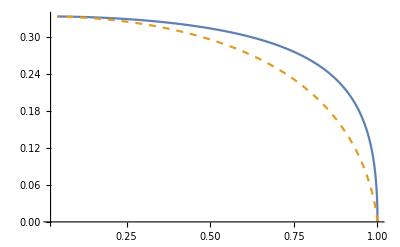

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo la sección transversal de absorción

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αx]^2/(6 Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[1]]+Cabs[a,b,c,nm,λ,λp,γ][[1]]
Cextx[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[2]]+Cabs[a,b,c,nm,λ,λp,γ][[2]]
Cextz[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[3]]+Cabs[a,b,c,nm,λ,λp,γ][[3]]
```

### Datos experimentales

```mathematica
Cabsexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2αx+ αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Cscaexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+ αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cextexp[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[1]]+Cabsexp[a,b,c,nm,λ,np][[1]]
Cextexpx[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[2]]+Cabsexp[a,b,c,nm,λ,np][[2]]
Cextexpz[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[3]]+Cabsexp[a,b,c,nm,λ,np][[3]]
```

```mathematica
Cextexp[30,10,10,1.33,144,1]
```

66.7352

## Cálculos

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
h vlight/300
```

4.13567

Se graficará la Cext promedio contrastada con las Cext individuales

```mathematica
qextAlDrpromedio=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
qextAlDrx=Table[{h vlight/λ,Cextx[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
qextAlDrz=Table[{h vlight/λ,Cextz[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicksCext=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorCext=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

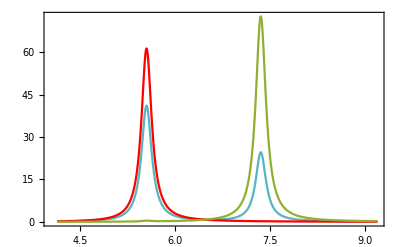

```mathematica
cextAl=ListLinePlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,Red],Style[qextAlDrz,RGBColor[0.560181,0.691569,0.194885]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.2]&/@{MaTeX["\langle C_{ext}"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.87,0.75}]]
```

```mathematica
Export["CextAlbueno.svg",cextAl]
```

CextAlbueno.svg

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAlDr=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl1Dr=Table[{h vlight/λ,Cext[1.75,1.75,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl2Dr=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl3Dr=Table[{h vlight/λ,Cext[2.25,2.25,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];qextEsferaDr=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
```

$Aborted

```mathematica
h vlight/5
```

248.14

```mathematica
upperTicksAl=Module[{labels,positions},labels={124,138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

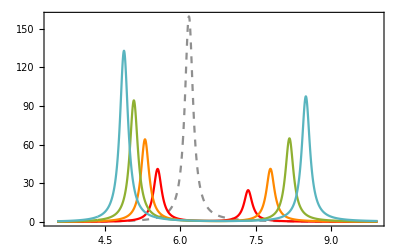

```mathematica
alc=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlDr,Red],Style[qextAl1Dr,RGBColor[1,0.533,0]],Style[qextAl2Dr,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3Dr,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["AR=1"],MaTeX["AR=1.5"],MaTeX["AR=1.75"],MaTeX["AR=2"],MaTeX["AR=2.5"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2}],{0.75,0.8}]]
```

```mathematica
Export["Alc.svg",alc]
```

Alc.svg

#### Misma razón de aspecto

```mathematica
qextAlAR=Table[{h vlight/λ,Cext[1.0,1.0,0.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl1AR=Table[{h vlight/λ,Cext[1.5,1.5,0.75,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl2AR=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl3AR=Table[{h vlight/λ,Cext[2.5,2.5,1.25,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl3sphere=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
```

```mathematica
h vlight/200
```

6.2035

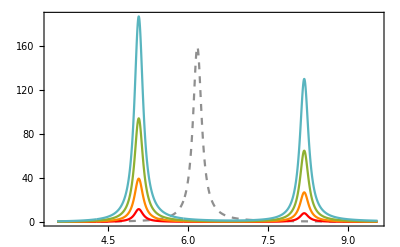

```mathematica
alAR=ListLinePlot[{Style[qextAl3sphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlAR,Red],Style[qextAl1AR,RGBColor[1,0.533,0]],Style[qextAl2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["a=2\mbox{ nm}"],MaTeX["a=1\mbox{ nm} "],MaTeX["a=1.5\mbox{ nm}"],MaTeX["a=2\mbox{ nm}"],MaTeX["a=2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},Spacings->{0.05},LegendLayout->{"Column",2}],{0.73,0.8}]]
```

```mathematica
Export["AlAR.svg",alAR]
```

AlAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAlcont=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.01}];
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.01}];
qextAlcont=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
```

```mathematica
h vlight/9
```

137.856

```mathematica
upperTicksAl=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

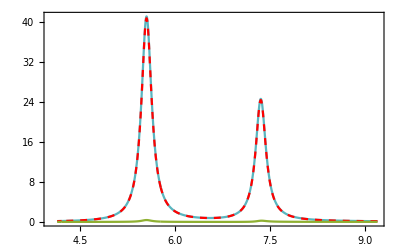

```mathematica
alcont=ListLinePlot[{Style[qextAlcont,RGBColor[0.349,0.71,0.749]],Style[qabsAlcont,Red,Dashed],Style[qscaAlcont,RGBColor[0.560181,0.691569,0.194885]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.2]&/@{MaTeX["C_{ext}"],MaTeX["C_{abs}"],MaTeX["C_{sca}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.85,0.75}]]
```

```mathematica
Export["AlContribuciones3.svg",alcont]
```

AlContribuciones3.svg

### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau11=Drop[Drop[au,{51,101}],1];
kau11=Drop[au,{1,52}];
λAu1=nau11[[All,1]]*1000; (*λ en nm*)
nau1=nau11[[All,2]];
kAu1=kau11[[All,2]];
nAu1=nau1+ I kAu1;
aU1=Transpose[{λAu1,nAu1}];
```

```mathematica
nindexau1=Interpolation[aU1];
```

```mathematica
300/(2*Pi*1.33)
```

35.8996

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAu1c=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu2c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu3c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu4c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAuEsferac=Table[{h vlight/λ,Cextexp[2,2,2.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qscaAu4c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,195,1937}];
qabsAu4c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,195,1937}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

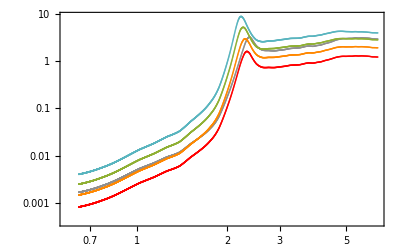

```mathematica
au1c=ListLogLogPlot[{Style[qextAuEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAu1c,Red],Style[qextAu2c,RGBColor[1,0.533,0]],Style[qextAu3c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu4c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["\mbox{AR}=1"],MaTeX["\mbox{AR}=1.5"],MaTeX["\mbox{AR}=1.75"],MaTeX["\mbox{AR}=2"],MaTeX["\mbox{AR}=2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",1}],{0.2,0.7}]]
```

```mathematica
Export["Auc.svg",au1c]
```

Auc.svg

```mathematica
N[Log10[10]]
```

1.

#### Misma razón de aspecto

```mathematica
qextAuAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAuEsferaAR=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
```

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

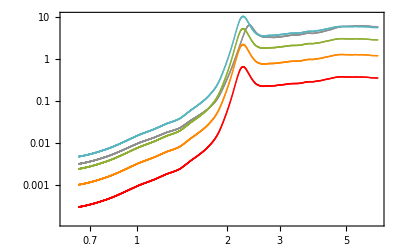

```mathematica
au1AR=ListLogLogPlot[{Style[qextAuEsferaAR,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAuAR,Red],Style[qextAu1AR,RGBColor[1,0.533,0]],Style[qextAu2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.05]&/@{MaTeX["a=2\mbox{ nm}"],MaTeX["a=1\mbox{ nm} "],MaTeX["a=1.5\mbox{ nm}"],MaTeX["a=2\mbox{ nm}"],MaTeX["a=2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.0,LegendLayout->{"Column",2}],{0.73,0.2}]]
```

```mathematica
Export["AuAR.svg",au1AR]
```

AuAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAucont=Table[{λ,Cabsexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qscaAucont=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qextAucont=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexau1[λ]]},{λ,300,800}];
```

```mathematica
h vlight/500
```

2.4814

```mathematica
upperTicks4=Module[{labels,positions},labels={0.8,0.85,0.9,0.95,1,1.1,1.2,1.3,1.4,1.5,1.7,2,2.3,2.5,3.1,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={0.8,0.85,0.95,1.15,1.25,1.35,1.45,1.55,1.6,1.65,1.75,1.85,2.1,2.3,2.6,2.8};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

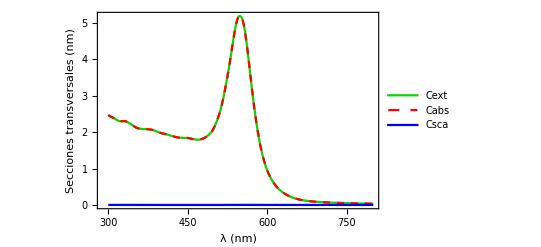

```mathematica
aucont=ListLinePlot[{Style[qextAucont,RGBColor[0.071,0.82,0]],Style[qabsAucont,Red,Dashed],Style[qscaAucont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AuContribuciones1.pdf",aucont]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

#### Oblato

```mathematica
qextAgc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAgEsferac=Table[{h vlight/λ,Cextexp[2.0,2.0,2.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
```

```mathematica
qabsAg3c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550,0.01}];
qscaAg3c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550,0.01}];
```

```mathematica
h vlight/3.241372910102672
```

382.77

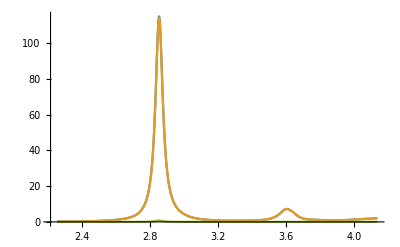

```mathematica
ListLinePlot[{qextAg3c,qabsAg3c,qscaAg3c},PlotRange->All]
```

```mathematica
h vlight/2.5
```

496.28

```mathematica
upperTicksAg=Module[{labels,positions},labels={310,355,414,496};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

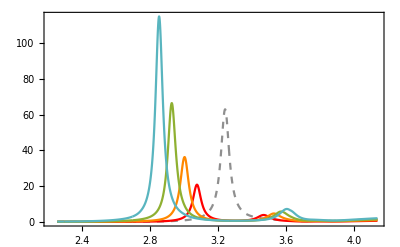

```mathematica
plata1c=ListLinePlot[{Style[qextAgEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgc,Red],Style[qextAg1c,RGBColor[1,0.533,0]],Style[qextAg2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["\mbox{AR}=1"],MaTeX["\mbox{AR}=1.5"],MaTeX["\mbox{AR}=1.75"],MaTeX["\mbox{AR}=2"],MaTeX["\mbox{AR}=2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["Agc.svg",plata1c]
```

Agc.svg

#### Misma razón de aspecto

```mathematica
qextAgAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,0.75,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
```

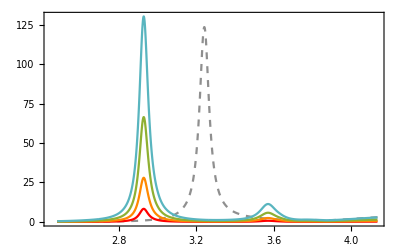

```mathematica
ag1AR=ListLinePlot[{Style[qextAg3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgAR,Red],Style[qextAg1AR,RGBColor[1,0.533,0]],Style[qextAg2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["a=2.5\mbox{ nm}"],MaTeX["a=1\mbox{ nm} "],MaTeX["a=1.5\mbox{ nm}"],MaTeX["a=2\mbox{ nm}"],MaTeX["a=2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["AgAR.svg",ag1AR]
```

AgAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAgcont=Table[{λ,Cabsexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qscaAgcont=Table[{λ,Cscaexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qextAgcont=Table[{λ,Cextexp[15,15,1,1.33,λ,nindexplata[λ]]},{λ,750,950}];
```

```mathematica
h vlight/950
```

1.306

```mathematica
upperTicksAg=Module[{labels,positions},labels={1.3,1.34,1.37,1.4,1.45,1.5,1.55,1.6,1.65};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={1.31,1.32,1.33,1.35,1.38,1.43,1.48,1.5,1.53,1.63};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

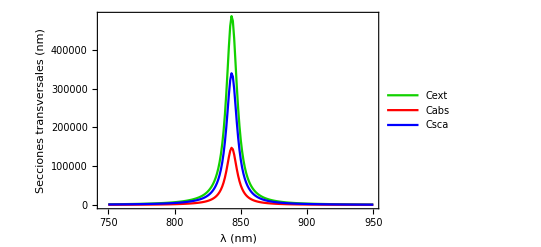

```mathematica
agcont=ListLinePlot[{Style[qextAgcont,RGBColor[0.071,0.82,0]],Style[qabsAgcont,Red],Style[qscaAgcont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AgContribuciones3.pdf",agcont]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
10/(2*Pi*1.33)
```

1.19665

```mathematica
λBism
```

#### Oblato

```mathematica
qextBic=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBi1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBi2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBi3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBiEsferac=Table[{h vlight/λ,Cextexp[2.25,2.25,2.25,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
```

```mathematica
h vlight/8.03042271067961
```

154.5

```mathematica
qextBiEsferac
```

{{80.0452,15.1883},{75.194,13.1289},{70.8972,11.5314},{67.0649,10.0444},{63.6257,8.94655},{60.522,8.22684},{57.707,7.58851},{55.1422,6.94876},{52.7958,6.26536},{50.6408,5.62404},{48.6549,4.79998},{46.8189,4.45677},{45.1164,4.10547},{43.5333,3.79226},{42.0576,3.55005},{40.6787,3.22359},{39.3873,2.91587},{38.1754,2.66525},{37.0358,2.48217},{35.9623,2.33929},{34.9493,2.20631},{33.9918,2.09661},{33.0853,2.01363},{32.226,1.94757},{31.4101,1.95543},{30.6346,2.01061},{29.8964,2.12549},{29.1929,2.23686},{28.5218,2.28546},{27.8809,2.49833},{27.2681,1.98188},{26.6817,1.88623},{26.12,1.99364},{25.5814,2.03037},{25.0647,2.18268},{24.5683,2.35421},{24.0913,1.13094},{23.6324,0.751201},{23.1907,0.826265},{22.7651,0.804508},{22.355,0.852595},{21.9593,0.849556},{21.5774,0.893297},{21.2086,0.938942},{20.8521,0.982766},{20.5074,1.02109},{20.174,1.05024},{19.8512,1.08461},{19.5386,1.13543},{19.2357,1.18991},{18.942,1.24805},{18.6571,1.3098},{18.3807,1.37505},{18.1124,1.44358},{17.8518,1.51825},{17.5986,1.59754},{17.3525,1.67898},{17.1131,1.76205},{16.8803,1.84627},{16.6537,1.9312},{16.4331,2.01642},{16.2183,2.10154},{16.009,2.18606},{15.8051,2.25986},{15.6063,2.33252},{15.4124,2.40426},{15.2233,2.47526},{15.0388,2.54571},{14.8587,2.61581},{14.6828,2.68571},{14.5111,2.75561},{14.3434,2.82565},{14.1794,2.89602},{14.0192,2.96685},{13.8626,3.03831},{13.7094,3.11054},{13.5596,3.18369},{13.413,3.25789},{13.2695,3.33328},{13.1291,3.40999},{12.9916,3.48815},{12.857,3.56787},{12.7251,3.64929},{12.5959,3.73252},{12.4693,3.81767},{12.3453,3.90484},{12.2236,3.99415},{12.1044,4.0857},{11.9874,4.17869},{11.8727,4.26987},{11.7602,4.36235},{11.6498,4.45608},{11.5414,4.55099},{11.435,4.64698},{11.3306,4.74396},{11.2281,4.84178},{11.1274,4.94032},{11.0284,5.03939},{10.9313,5.13882},{10.8358,5.23841},{10.742,5.33792},{10.6498,5.43713},{10.5592,5.53576},{10.47,5.63353},{10.3824,5.73017},{10.2963,5.82534},{10.2115,5.91874},{10.1282,6.01002},{10.0462,6.09885},{9.96546,6.18842},{9.88606,6.27955},{9.80791,6.36885},{9.73098,6.45613},{9.65526,6.54121},{9.5807,6.6239},{9.50728,6.70404},{9.43498,6.78147},{9.36378,6.85602},{9.29364,6.92757},{9.22454,6.99599},{9.15646,7.06117},{9.08938,7.12301},{9.02327,7.18143},{8.95812,7.23637},{8.89391,7.28777},{8.83061,7.33562},{8.7682,7.37988},{8.70667,7.42057},{8.646,7.4577},{8.58616,7.4913},{8.52715,7.52142},{8.46894,7.54812},{8.41153,7.57147},{8.35488,7.59157},{8.299,7.6085},{8.24386,7.62238},{8.18944,7.63333},{8.13574,7.64147},{8.08274,7.64694},{8.03042,7.64986},{7.97878,7.64209},{7.9278,7.62247},{7.87746,7.59902},{7.82776,7.57189},{7.77869,7.54126},{7.73022,7.50727},{7.68235,7.4701},{7.63508,7.42993},{7.58838,7.38693},{7.54225,7.34128},{7.49668,7.29315},{7.45165,7.24273},{7.40717,7.1902},{7.36321,7.13571},{7.31977,7.07946},{7.27683,7.0216},{7.2344,6.96229},{7.19247,6.9017},{7.15101,6.83997},{7.11003,6.77726},{7.06952,6.7137},{7.02946,6.64944},{6.98986,6.58459},{6.9507,6.51928},{6.91198,6.45363},{6.87369,6.38775},{6.83581,6.32174},{6.79836,6.2557},{6.76131,6.18973},{6.72466,6.1239},{6.68841,6.05831},{6.65255,5.99302},{6.61707,5.9281},{6.58196,5.86362},{6.54723,5.79964},{6.51286,5.73622},{6.47885,5.6734},{6.4452,5.61122},{6.41189,5.54975},{6.37892,5.489},{6.34629,5.42902},{6.314,5.36984},{6.28203,5.31148},{6.25038,5.25398},{6.21905,5.19735},{6.18803,5.14161},{6.15732,5.08679},{6.12692,5.0329},{6.09681,4.97994},{6.06699,4.92794},{6.03747,4.87691},{6.00823,4.82684},{5.97928,4.78411},{5.9506,4.74287},{5.9222,4.70239},{5.89406,4.66265},{5.8662,4.62364},{5.83859,4.58535},{5.81124,4.54777},{5.78415,4.51089},{5.75731,4.47468},{5.73072,4.43915},{5.70437,4.40428},{5.67826,4.37005},{5.65239,4.33646},{5.62676,4.30349},{5.60136,4.27114},{5.57618,4.23939},{5.55123,4.20823},{5.5265,4.17765},{5.502,4.14764},{5.47771,4.11819},{5.45363,4.08929},{5.42976,4.06094},{5.4061,4.03311},{5.38265,4.00581},{5.3594,3.97902},{5.33635,3.95274},{5.31349,3.92696},{5.29083,3.90166},{5.26837,3.87685},{5.24609,3.85251},{5.224,3.82864},{5.2021,3.80523},{5.18038,3.78227},{5.15884,3.75976},{5.13748,3.73768},{5.11629,3.71604},{5.09528,3.69483},{5.07444,3.67404},{5.05377,3.65367},{5.03327,3.6337},{5.01293,3.61415},{4.99276,3.59617},{4.97275,3.57976},{4.9529,3.56373},{4.9332,3.54808},{4.91366,3.53279},{4.89428,3.51785},{4.87505,3.50325},{4.85597,3.48899},{4.83704,3.47504},{4.81825,3.46141},{4.79961,3.44809},{4.78112,3.43505},{4.76277,3.4223},{4.74455,3.40983},{4.72648,3.39763},{4.70854,3.38568},{4.69074,3.37398},{4.67307,3.36253},{4.65554,3.35131},{4.63813,3.34032},{4.62086,3.32954},{4.60371,3.31898},{4.58669,3.30862},{4.5698,3.29846},{4.55303,3.28848},{4.53638,3.27869},{4.51986,3.26908},{4.50345,3.25963},{4.48716,3.25034},{4.47099,3.24121},{4.45494,3.23222},{4.439,3.22338},{4.42317,3.21468},{4.40746,3.2061},{4.39186,3.19765},{4.37637,3.18932},{4.36099,3.18109},{4.34571,3.17298},{4.33054,3.16496},{4.31548,3.15704},{4.30052,3.14922},{4.28567,3.14147},{4.27091,3.1338},{4.25626,3.12621},{4.24171,3.11869},{4.22726,3.11123},{4.2129,3.10383},{4.19865,3.09649},{4.18449,3.08919},{4.17042,3.08194},{4.15645,3.07474},{4.14257,3.06756},{4.12879,3.06042},{4.11509,3.05331},{4.10149,3.04622},{4.08797,3.03915},{4.07455,3.0321},{4.06121,3.02506},{4.04796,3.01803},{4.0348,3.011},{4.02172,3.00397},{4.00872,2.99695}}

```mathematica
h vlight/0.1
```

12407.

```mathematica
h vlight/50
```

24.814

```mathematica
upperTicksBi=Module[{labels,positions},labels={25,62,124,248};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

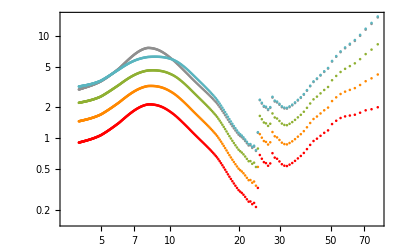

```mathematica
Bismuto1c=ListLogLogPlot[{Style[qextBiEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBic,Red],Style[qextBi1c,RGBColor[1,0.533,0]],Style[qextBi2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.05]&/@{MaTeX["\mbox{AR}=1"],MaTeX["\mbox{AR}=1.5"],MaTeX["\mbox{AR}=1.75"],MaTeX["\mbox{AR}=2"],MaTeX["\mbox{AR}=2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2}],{0.26,0.15}]]
```

```mathematica
Export["Bic.svg",Bismuto1c]
```

Bic.svg

#### Misma razón de aspecto

```mathematica
qextBiAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
```

```mathematica
h vlight/120
```

10.3392

```mathematica
1.75/2
```

0.875

```mathematica
Graphics[{Pink,Disk[]},PlotRange->{{-.5,.5},{0,1.5}},PlotRangeClipping->True,Frame->True]
```

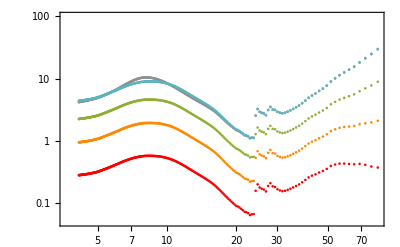

```mathematica
BiAR=ListLogLogPlot[{Style[qextBi3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBiAR,Red],Style[qextBi1AR,RGBColor[1,0.533,0]],Style[qextBi2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->{0.05,100},PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["a=2.5\mbox{ nm}"],MaTeX["a=1\mbox{ nm} "],MaTeX["a=1.5\mbox{ nm}"],MaTeX["a=2\mbox{ nm}"],MaTeX["a=2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",3}],{0.45,0.83}]]
```

```mathematica
Export["BisAR.svg",BiAR]
```

BisAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsBicont=Table[{λ,Cabsexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qscaBicont=Table[{λ,Cscaexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qextBicont=Table[{λ,Cextexp[2,2,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,500}];
```

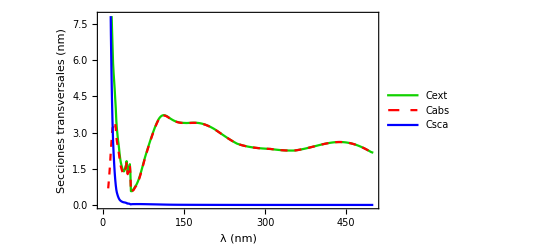

```mathematica
Bismutocont=ListLinePlot[{Style[qextBicont,RGBColor[0.071,0.82,0]],Style[qabsBicont,Red,Dashed],Style[qscaBicont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["BiContribuciones1.pdf",Bismutocont]
```

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

#### Oblato

```mathematica
qextMgOc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgOcsphere=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
```

```mathematica
Table[{Cabsexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}},{{0.,0.,0.}}}

```mathematica
h c/1200
```

1.03392

```mathematica
upperTicksMgO=Module[{labels,positions},labels={1,1.2,1.5,2.1,3.1,6.2};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorMgO=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

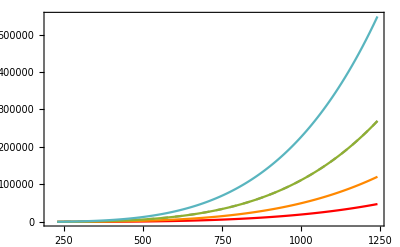

```mathematica
MgO1=ListLinePlot[{Style[qextMgOcsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOc,Red],Style[qextMgO1c,RGBColor[1,0.533,0]],Style[qextMgO2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.05]&/@{MaTeX["\mbox{AR}=1"],MaTeX["\mbox{AR}=1.5"],MaTeX["\mbox{AR}=1.75"],MaTeX["\mbox{AR}=2"],MaTeX["\mbox{AR}=2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2}],{0.32,0.8}]]
```

```mathematica
Export["MgOc.svg",MgO1]
```

MgOc.svg

```mathematica
qextMgOAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
```

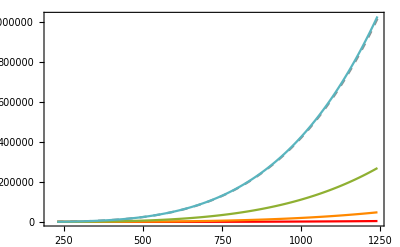

```mathematica
MgO2=ListLinePlot[{Style[qextMgO3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOAR,Red],Style[qextMgO1AR,RGBColor[1,0.533,0]],Style[qextMgO2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["a=2.5\mbox{ nm}"],MaTeX["a=1\mbox{ nm} "],MaTeX["a=1.5\mbox{ nm}"],MaTeX["a=2\mbox{ nm}"],MaTeX["a=2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2}],{0.33,0.8}]]
```

```mathematica
Export["MgOAR.svg",MgO2]
```

MgOAR.svg

## Eritrocitos

```mathematica
RBCreal=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NRealRBC.csv"];
RBCimag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NImagRBC.csv"];
```

```mathematica
λRBC=RBCreal[[All,1]];
nRBC=RBCreal[[All,2]];
kRBC=RBCimag[[All,2]];
nindRBC=nRBC+ I kRBC;
RBC=Transpose[{λRBC,nindRBC}];
```

```mathematica
nindexRBC=Interpolation[RBC];
```

```mathematica
qabsRBC=Table[{λ,Cabsexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qscaRBC=Table[{λ,Cscaexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexp[20,20,12,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpx[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpz[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
```

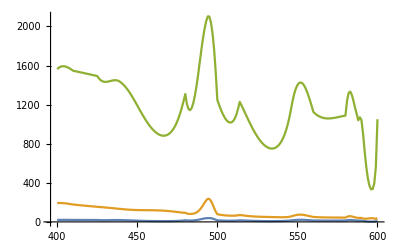

```mathematica
ListLinePlot[{qextRBC,qscaRBC,qabsRBC}]
```

```mathematica
nRBC
```

{1.383,1.365,1.363,1.364,1.365,1.367,1.36481,1.378,1.3728,1.3721,1.361,1.383,1.36053,1.37,1.357,1.3687,1.3668,1.356,1.3667,1.35724,1.356,1.3666}

```mathematica
kRBC
```

{1.4006,1.4007,1.4019,1.404,1.4043,1.4005,1.3993,1.3983,1.3975,1.3973,1.3973,1.3974,1.3974,1.398,1.3978,1.3976,1.3983,1.3975,1.3973,1.39729,1.39728,1.3971}

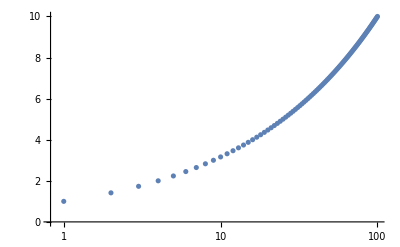

```mathematica
ListLogLinearPlot[Table[{n,Sqrt[n]},{n,100}]]
```

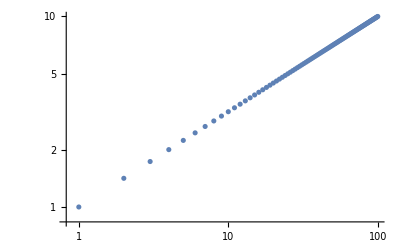

```mathematica
ListLogLogPlot[Table[{n,Sqrt[n]},{n,100}]]
```

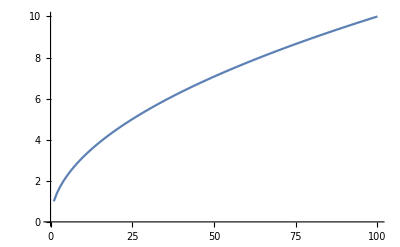

```mathematica
ListLinePlot[Table[{n,Sqrt[n]},{n,100}]]
```